0.4

-1

1

0.16 (-1.+6.25 t+1. t^2)

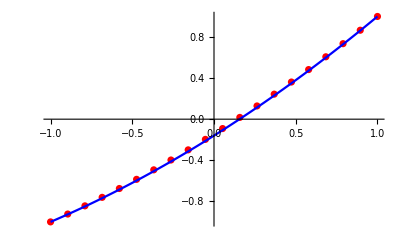

```mathematica
(*а-ка лямбда*)l = 0.4
a =-1
b = 1 
(*Ядро*)K[t_,s_] := (t^2-1)*s^3;
(*Точное решение*)sol1=DSolveValue[x[t]-l*Integrate[K[t,s]*x[s], {s, a, b}] == t, x[t], t]

(*Лист точек х*)x1 ={-1,-0.894737,-0.789474,-0.684211,-0.578947,-0.473684,-0.368421,-0.263158,-0.157895,-0.0526316,0.0526316,0.157895,0.263158,0.368421,0.473684,0.578947,0.684211,0.789474,0.894737,1};
(*Лист точек f(x)*)fx1={-1,-0.923533,-0.843866,-0.760999,-0.674933,-0.585668,-0.493202,-0.397538,-0.298674,-0.19661,-0.091347,0.0171157,0.128778,0.24364,0.361701,0.482962,0.607422,0.735082,0.865941,1};
p1=ListPlot[Transpose[{x1,fx1}],PlotStyle->Red];
p2=Plot [sol1, {t, -1, 1}, PlotStyle->Blue];
(*Итоговый график*)Show[p1,p2]
```

```mathematica
maxValKernel = NMaxValue[{Abs[K[x,y]], a≤x≤b, a≤y≤b}, {x,y}]  
limitation = 1/(maxValKernel*(b-a))
Plot3D[Abs[K[t,s]], {t, a, b}, {s, a, b}, AxesLabel->{t, s, k}]
```

1.

0.5

-Graphics3D-